This mathematica code solves the differential equation for the height of the interface between the free liquid phase and the gel of particles. 
The differential equation can be found in the paper by Alexis Darras et al. named: “Erythrocyte sedimentation:Fracture and collapse of a high-volume-fraction soft-colloid gel”.

```mathematica
Clear["Global`*"]
(*Initial conditions:*)
phi0=4/10; (*initial colloid volume fraction*)
h0=4; (*[cm] initial height of the interface*)
drho=80*10^(-6); (*[kg/cm^3] density difference between the colloids and the suspending medium*)
g=981; (*[cm/s^2] gravitational acceleration*)
gamma=0.48*10^(-8);(*=a^2/kappa_0 in [cm^2] with a the characteristic size of the gels pores, and kappa_0 a scaling constant*) 
eta=0.000012; (*[kg/(cm s)]suspending medium viscosity*)
phim=86/100; (*maximum colloid volume fraction*)
hm=h0*phi0/phim ;(*minimum height of the interface*)

(*Solve the differential equation:*)
hsol=NDSolveValue[{h'[t]==-(drho*g*gamma)*((phim-phi0*h0/(h[t]))^3)/(eta*(phi0*h0/(h[t]))*(1-phi0*h0/(h[t]))),h[0]==h0},h,{t,0,10^12}]
```

InterpolatingFunction[…]

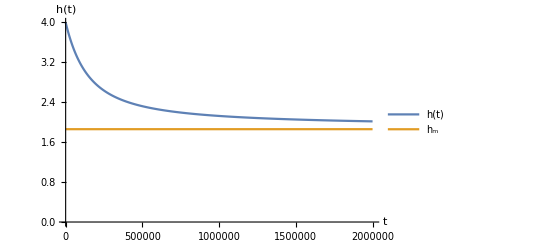

```mathematica
(*Plot:*)
tfinal=2*10^6;
p1=Plot[{hsol[t],hm},{t,0,tfinal},PlotRange->{0,h0},AxesLabel->{t,h[t]},PlotPoints->1000,(*PlotLabel->"Height of the interface",*)PlotLegends->{"h(t)",Subscript[h,m]},LabelStyle->Directive[FontSize->14]]
```

```mathematica
(*Export picture:*)
Export[NotebookDirectory[]<>"1D_h(t)_plot.png",p1,ImageResolution->1000]
```

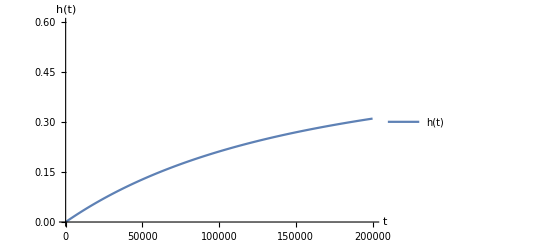

```mathematica
(*Plot (h0-h(t))/h0:*)
tfinal=2*10^5;
p1=Plot[{(h0-hsol[t])/h0},{t,0,tfinal},PlotRange->{0,0.6},AxesLabel->{t,h[t]},PlotPoints->1000,(*PlotLabel->"Height of the interface",*)PlotLegends->{"h(t)"},LabelStyle->Directive[FontSize->14]]
```

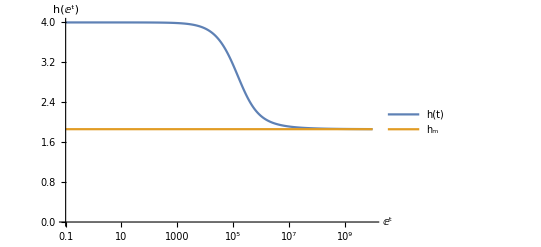

```mathematica
(*Log plot*)
tfinal=10^10;
p2=LogLinearPlot[{hsol[t],hm},{t,0.1,tfinal},PlotRange->{0,h0},AxesLabel->{t,h[t]},PlotPoints->1000,PlotLegends->{"h(t)",Subscript[h,m]},LabelStyle->Directive[FontSize->14]]
```

```mathematica
(*Export picture:*)
Export[NotebookDirectory[]<>"1D_h(t)_Logplot.png",p2,ImageResolution->1000]
```

```mathematica
(*Make animation:*)
film=Animate[Plot[hsol[t],{x,0,1},PlotRange->{0,h0+0.1},Filling->Bottom,FillingStyle->Darker[Blue,phi0*h0/hsol[t]
],AxesLabel->{x,"h(t)"},PlotLegends->{BarLegend[{{Blue,Black},{0,1}},LegendLabel->"ϕ(t)"],t"=t"},PlotLabel->"Height of interface"],{t,0,2*10^5}]
```

```mathematica
(*Export animation*)
Export[NotebookDirectory[]<>"1D_h(t)_animate.gif",film]
```

C:\Users\myrth\OneDrive\Bureaublad\scriptie\h(t)\1D_h(t)_animate.gif